#### Simulation Code

Np = number of particles
L = Length of ring
Tstep = Number of time updates in one second
Pjump = Probability that a particle jumps
Tfinal = time at the end of the simulation

```mathematica
Np=5;
L=10;
Tstep = 10; 
Pjump = 1/Tstep;
Tfinal=2;
```

```mathematica
Jump[X_, k_]:=Module[{Y, L,j},
L = Length[X];
Y =X;
j = Mod[k,L]+1;
If[X[[k]]==0, Return[Y]];
If[X[[j]]==1, Return[Y]];
Y[[k]] =0;
Y[[j]]=1;
Return[Y];
]
```

```mathematica
Jump[{0, 1, 1}, 1]
```

{0,1,1}

```mathematica
RandomVariate[BernoulliDistribution[Pjump], L]
```

{0,0,0,0,0,0,1,0,0,1}

```mathematica
RandomEnviroment = Table[RandomVariate[BernoulliDistribution[Pjump], L], {t, 1, Tfinal*Tstep}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,1,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,1,0,0,0,0,0,0,1,0},{0,1,1,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,1},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,1,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,1,0}}

```mathematica
SeqUpdate[X_, C_]:= Module[{Y, L, i},
L = Length[X];
Y = X;
Do[If[C[[k]]==1, Y =Jump[Y, k] ], {k, L}];
Return[Y]
]
```

```mathematica
SeqUpdate[Xinitial, RandomEnviroment[[17]]]
```

{0,0,0,1,1,1,1,0,1,0}

```mathematica
Xinitial = {0, 0,0,1, 1, 1, 1, 1, 0, 0};
```

```mathematica
Sim[Xi_, Tf_, Ts_]:=Module[{Pj ,Xhist, t, RE, L},
Pj = 1/Ts;
L = Length[Xi];
Xhist = {Xi};
RE = Table[RandomVariate[BernoulliDistribution[Pj], L], {t, 1, Tf*Ts}];
Do[AppendTo[Xhist, SeqUpdate[Last[Xhist], RE[[t]]]], {t, Tf* Ts}];
Return[Xhist]
]
```

```mathematica
Sim[Xinitial, Tfinal, Tstep]
```

{{0,0,0,1,1,1,1,1,0,0},{0,0,0,1,1,1,1,1,0,0},{0,0,0,1,1,1,1,1,0,0},{0,0,0,1,1,1,1,1,0,0},{0,0,0,1,1,1,1,0,1,0},{0,0,0,1,1,1,1,0,1,0},{0,0,0,1,1,1,1,0,1,0},{0,0,0,1,1,1,1,0,1,0},{0,0,0,1,1,1,1,0,0,1},{0,0,0,1,1,1,1,0,0,1},{0,0,0,1,1,1,1,0,0,1},{0,0,0,1,1,1,0,1,0,1},{0,0,0,1,1,1,0,1,0,1},{0,0,0,1,1,1,0,1,0,1},{0,0,0,1,1,1,0,1,0,1},{0,0,0,1,1,1,0,1,0,1},{0,0,0,1,1,1,0,1,0,1},{0,0,0,1,1,1,0,1,0,1},{1,0,0,1,1,1,0,1,0,0},{0,1,0,1,1,1,0,1,0,0},{0,1,0,1,1,1,0,1,0,0}}

```mathematica
Nl=300;
```

```mathematica
SimAvg = N[Sum[Sim[Xinitial, Tfinal, Tstep]/Nl, {i, 1, Nl}]]
```

{{0.,0.,0.,1.,1.,1.,1.,1.,0.,0.},{0.00666667,0.,0.,1.,1.,1.,1.,0.883333,0.1,0.01},{0.01,0.,0.,1.,1.,1.,0.983333,0.8,0.183333,0.0233333},{0.01,0.,0.,1.,1.,1.,0.97,0.733333,0.233333,0.0533333},{0.0233333,0.,0.,1.,1.,1.,0.923333,0.696667,0.283333,0.0733333},{0.03,0.,0.,1.,1.,0.996667,0.89,0.686667,0.296667,0.1},{0.0566667,0.,0.,1.,1.,0.996667,0.85,0.65,0.323333,0.123333},{0.0766667,0.00666667,0.,1.,1.,0.983333,0.823333,0.62,0.363333,0.126667},{0.08,0.0166667,0.,1.,0.996667,0.97,0.816667,0.6,0.376667,0.143333},{0.0933333,0.0266667,0.,1.,0.986667,0.953333,0.8,0.6,0.376667,0.163333},{0.103333,0.03,0.00666667,1.,0.986667,0.936667,0.763333,0.593333,0.416667,0.163333},{0.11,0.0366667,0.0133333,1.,0.98,0.923333,0.75,0.603333,0.39,0.193333},{0.126667,0.0366667,0.0166667,0.996667,0.983333,0.896667,0.753333,0.573333,0.42,0.196667},{0.133333,0.0433333,0.02,0.993333,0.976667,0.853333,0.783333,0.55,0.423333,0.223333},{0.156667,0.0433333,0.0333333,0.993333,0.963333,0.853333,0.74,0.583333,0.4,0.233333},{0.166667,0.0533333,0.0366667,0.983333,0.953333,0.856667,0.726667,0.583333,0.39,0.25},{0.173333,0.05,0.0533333,0.973333,0.943333,0.843333,0.716667,0.573333,0.396667,0.276667},{0.176667,0.06,0.06,0.96,0.946667,0.82,0.69,0.596667,0.383333,0.306667},{0.2,0.0733333,0.06,0.96,0.93,0.79,0.703333,0.606667,0.36,0.316667},{0.21,0.0833333,0.07,0.956667,0.906667,0.803333,0.686667,0.576667,0.41,0.296667},{0.22,0.09,0.0866667,0.943333,0.906667,0.776667,0.71,0.543333,0.42,0.303333}}

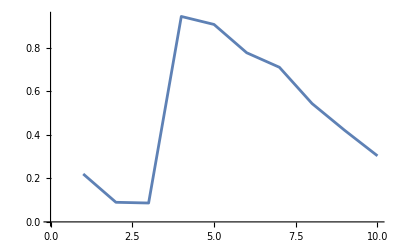

```mathematica
ListPlot[Last[SimAvg], Joined->True]
```

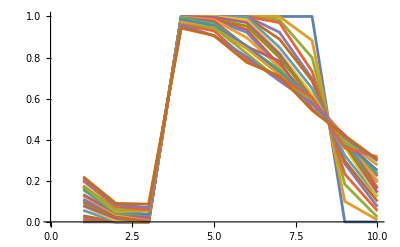

```mathematica
ListPlot[SimAvg, Joined->True]
```

```mathematica
SimAvgAdj = Flatten[Table[{k/L, t/Tstep,SimAvg[[t]][[k]]}, {t, 1, Length[SimAvg]},{k, 1, L} ], 1];
```

```mathematica
ListPlot3D[SimAvgAdj]
```

-Graphics3D-

```mathematica
ListDensityPlot[SimAvgAdj]
```

-Graphics-

#### Large N and L, zero speed shock

Np = number of particles
L = Length of ring
Tstep = Number of time updates in one second
Pjump = Probability that a particle jumps
Tfinal = time at the end of the simulation

```mathematica
Np=50;
L=101;
Tstep = 20; 
Pjump = 1/Tstep;
Tfinal=100;
```

```mathematica
Xinitial = Table[If[i> Np/2 && i < 3 Np/2,1,0], {i,1, L}];
```

```mathematica
Ntrials=200;
```

```mathematica
SimAvg = N[Sum[Sim[Xinitial, Tfinal, Tstep]/Ntrials, {i, 1, Ntrials}]];
```

```mathematica
SimAvgProc = Flatten[Table[{k/L, t/Tstep,SimAvg[[t]][[k]]}, {t, 1, Length[SimAvg]},{k, 1, L} ], 1];
```

```mathematica
ListPlot3D[SimAvgProc]
```

-Graphics3D-

```mathematica
ListDensityPlot[SimAvgProc, PlotLegends->Automatic]
```

-Graphics-

#### Large N and L, non-zero speed shock

Np = number of particles
L = Length of ring
Tstep = Number of time updates in one second
Pjump = Probability that a particle jumps
Tfinal = time at the end of the simulation

```mathematica
Np=25;
L=101;
M= (L-Np)/2;
Tstep = 20; 
Pjump = 1/Tstep;
Tfinal=100;
```

```mathematica
Xinitial = Table[If[i> M && i < M+ Np,1,0], {i,1, L}];
```

```mathematica
Ntrials=200;
```

```mathematica
SimAvg = N[Sum[Sim[Xinitial, Tfinal, Tstep]/Ntrials, {i, 1, Ntrials}]];
```

```mathematica
SimAvgProc = Flatten[Table[{ t/Tstep, k,SimAvg[[t]][[k]]}, {t, 1, Length[SimAvg]},{k, 1, L} ], 1];
```

```mathematica
ListPlot3D[SimAvgProc]
```

-Graphics3D-

```mathematica
Hplot2 =ListDensityPlot[SimAvgProc, PlotLegends->Automatic]
```

-Graphics-

```mathematica
v=1 - (2Np/L)
```

51/101

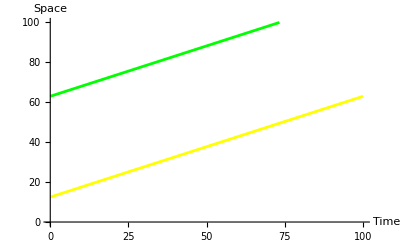

```mathematica
SpeedPlot = Plot[{v t +Np +M, v t +Np +M - (L/2)} , {t, 0, 100}, PlotRange->{{0,100},{0, 100}}, PlotStyle->{Green, Yellow}, AxesLabel->{"Time", "Space"}]
```

```mathematica
Show[Hplot2, SpeedPlot]
```

-Graphics-

```mathematica
Xinitial[[M+Np]]
```

0

```mathematica
Np +M - L
```

-38